```mathematica
Lab 3
Variant 5
```

```mathematica
Euler[u0_, u01_, a_, b_, h_, p_, q_, f_]:= Block[{X, Y, Y1, k, n, Res},
n=(b-a)/h;
X={};
For[k=0, k<n, k++,
AppendTo[X,a+k*h //N](* Сформировали сетку Х *)
];
Y={ u0};
Y1={ u01};
For[k=1, k<n, k++,
AppendTo[Y,0]; 
AppendTo[Y1,0]; 
];
For[k=1, k<n, k++,
Y1⟦k+1⟧=Y1⟦k⟧+h*(-p[X⟦k⟧]*Y1⟦k⟧ + q[X⟦k⟧]*Y⟦k⟧ + f[X⟦k⟧])//N; 
Y⟦k+1⟧=Y⟦k⟧+h*Y1⟦k⟧//N; 
];
Res={};
AppendTo[Res, X];
AppendTo[Res, Y];
AppendTo[Res, Y1];
Return[Res];
];
```

```mathematica
u[x_]:= x*Sin[x];

p[x_]:= 2*x;
q[x_]:= 1;
f[x_]:= 2*(x^2+1)*Cos[x];
a=0;
b=0.5;
n=100;
h=(b-a)/n;
(* Для Z, Z' *)
u0 = 0;
u1 = 0;
Res = Euler[u0,u1,a,b,h,p,q,f];
X = Res⟦1⟧;
Z0 = Res⟦2⟧;
Z01 = Res⟦3⟧;

(* Для Z1, Z1' *)
u0 = 0;
u1 = 1;
f[x_]:=0;
Res = Euler[u0,u1,a,b,h,p,q,f];
Z10 = Res⟦2⟧;
Z11 = Res⟦3⟧;

(* Для Z2, Z2' *)
u0 = 1;
u1 = 0;
Res = Euler[u0,u1,a,b,h,p,q,f];
Z20 = Res⟦2⟧;
Z21 = Res⟦3⟧;

α0 = 1;
β0 = 0;
γ0 = 0;
α1 = 1;
β1 = 0;
γ1 = 1/2*Sin[1/2]; //N

U0=Z0+C1*Z10 + C2*Z20;
U1=Z01+C1*Z11 + C2*Z21;

(* Находим коэффициенты C1 и C2 *)
Solution= Solve[α0*U0⟦1⟧+β0*U1⟦1⟧==γ0&& α1*U0⟦-1⟧+β1*U1⟦-1⟧==γ1, {C1, C2}];
C1 = C1/.Solution;
C2 = C2/.Solution⟦1⟧;

U0 = U0 //Flatten ;

(* ЕСЛИ НЕ ХОЧЕТ РАБОТАТЬ С ПЕРВОГО РАЗА, то перезагрузить ядро и выполнить. Может даже несколько раз *)
```

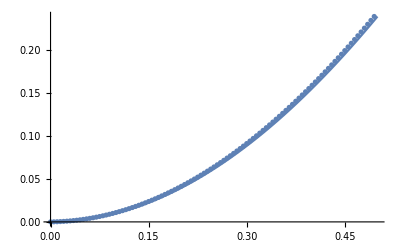

```mathematica
G1 = Plot[u[x], {x,a, b}];
G2 = ListPlot[Transpose[{X,U0}]];
Show[G1, G2]
```